# Ejercicio I.3: Simulación de elementos de la red

## Nombre del Alumno: Felix Sanz González DNI: 78997168B

# -Graphics-

# 1.- Generacion de paquetes, y transmisiones. Abstracción de un enlace

```mathematica
Clear["Global`*"]
err = 0.1;
npaquetes = 1000;
lambda = 2000;
a = 2;

p = 0.2;
mu = 3000;
TiSW = 1/mu;
TpSW =(a*TiSW-TiSW)/2 
c = 3200000;
l = c/mu//N
```

1/6000

1066.67

```mathematica
RndExp[ratio_] := -Log[RandomReal[]]/ratio//N;
```

```mathematica
RndExp[lambda]
```

0.000410488

```mathematica
GetArrivals[transmisionlista_,tp_]:=Map[(If[#[[4]]==0,#[[1]]+#[[2]]+tp,Unevaluated[Sequence[]]])&,transmisionlista];
```

```mathematica
(*Source[tentrellegadas_,len_,idFlow_,period_,idIn_:0]:=*)
createPackets[lambda_,len_,idFlow_,period_,idIn_]:= 
Module[{checktime =0, n =1, lista = {idIn}},
NestWhileList[({checktime += RndExp[lambda], RndExp[1/l],n,0,0,n++,idFlow,lista,checktime})&, 
{checktime += RndExp[lambda], RndExp[1/l],n,0,0,n++,idFlow,lista,checktime}, (#[[1]]< period)&]];
```

```mathematica
paquetes = createPackets[lambda,l,1,1,0];
paquetes[[1;;5]]
```

{{0.00220122,1505.6,1,0,0,1,1,{0},0.00220122},{0.00350255,515.273,2,0,0,2,1,{0},0.00350255},{0.00514573,157.965,3,0,0,3,1,{0},0.00514573},{0.00537871,938.844,4,0,0,4,1,{0},0.00537871},{0.00537916,1.74051,5,0,0,5,1,{0},0.00537916}}

```mathematica
(* pkt={chkTime,length,nseqLink,error,nrtx,nseqFlow,flowId,{path},{timePath}} *)

createTx[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
None;
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
]

createTxSW[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
AppendTo[listTx,{checkTime,pck[[2]],n,1,nrtx++,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
];

createTxGBN[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
AppendTo[listTx,{checkTime,pck[[2]],n,1,nrtx++,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c);n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
]
```

```mathematica
paquetesNormales = createTx[paquetes,p,TpSW,c];
```

```mathematica
paquetesNormales⟦1;;5⟧
```

{{0.00220122,1505.6,1,0,0,1,1,{0},0.00220122},{0.00350255,515.273,2,0,0,2,1,{0},0.00350255},{0.00514573,157.965,3,0,0,3,1,{0},0.00514573},{0.00552843,938.844,4,0,0,4,1,{0},0.00537871},{0.00615515,1.74051,5,0,0,5,1,{0},0.00537916}}

```mathematica
paquetesSW = createTxSW[paquetes,p,TpSW,c];
paquetesSW[[1;;5]]
```

{{0.00220122,1505.6,1,0,0,1,1,{0},0.00220122},{0.00350255,515.273,2,0,0,2,1,{0},0.00350255},{0.00514573,157.965,3,0,0,3,1,{0},0.00514573},{0.00552843,938.844,4,0,0,4,1,{0},0.00537871},{0.00615515,1.74051,5,0,0,5,1,{0},0.00537916}}

```mathematica
paquetesGBN = createTxGBN[paquetes,p,TpSW,c];
paquetesGBN[[1;;5]]
```

{{0.00220122,1505.6,1,0,0,1,1,{0},0.00220122},{0.00350255,515.273,2,1,0,2,1,{0},0.00350255},{0.0039969,515.273,2,0,1,2,1,{0},0.00350255},{0.00514573,157.965,3,0,0,3,1,{0},0.00514573},{0.00537871,938.844,4,0,0,4,1,{0},0.00537871}}

```mathematica
Get["C:\\Users\\felix\\Desktop\\Todo\\U.P.V\\MASTER\\Segundo\\Asignaturas\\Rendimiento en Redes de Telecomunicacion\\Casos\\Caso I\\drawTxPRM2024.m"];
```

```mathematica
?drawTxPRM2024`*
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesNormales]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesSW]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
(*Poner 0.005 en WW*)
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesGBN]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
(*Poner 0.004 en WW*)
```

```mathematica
(*Tenemos que conseguir hacer una lista de paquetes que no contenga los paquetes erroneos --> Filtrar *)
(*Esta funcion tambien se encargará de actualizar el tiempo de llegada del paquete*)

filtrarPaquetes[paquetes_,c_,Tp_]:=Map[
(If[#[[4]] == 0,{#[[1]]+#[[2]]/c+Tp, #[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]},Nothing])
&,paquetes]
```

```mathematica
paquetesbuenosNormales = filtrarPaquetes[paquetesNormales,c,TpSW];
paquetesNormales[[1;;20]]
paquetesbuenosNormales[[1;;20]]
paquetesbuenosSW = filtrarPaquetes[paquetesSW,c,TpSW];
paquetesSW[[1;;20]]
paquetesbuenosSW[[1;;20]]
paquetesbuenosGBN = filtrarPaquetes[paquetesGBN,c,TpSW];
paquetesGBN[[1;;20]]
paquetesbuenosGBN[[1;;10]]
```

{{0.00220122,1505.6,1,0,0,1,1,{0},0.00220122},{0.00350255,515.273,2,0,0,2,1,{0},0.00350255},{0.00514573,157.965,3,0,0,3,1,{0},0.00514573},{0.00552843,938.844,4,0,0,4,1,{0},0.00537871},{0.00615515,1.74051,5,0,0,5,1,{0},0.00537916},{0.00648903,217.374,6,0,0,6,1,{0},0.00632819},{0.00689029,579.314,7,0,0,7,1,{0},0.00649131},{0.00740466,362.501,8,0,0,8,1,{0},0.00684038},{0.00801213,2100.56,9,0,0,9,1,{0},0.00801213},{0.00900189,1135.31,10,0,0,10,1,{0},0.00813912},{0.00969,566.711,11,0,0,11,1,{0},0.00838099},{0.0102004,6330.69,12,0,0,12,1,{0},0.00896664},{0.0125121,19.2149,13,0,0,13,1,{0},0.0089917},{0.0128514,711.361,14,0,0,14,1,{0},0.00902584},{0.0134071,1250.51,15,0,0,15,1,{0},0.00965522},{0.0141312,21.4374,16,0,0,16,1,{0},0.0106984},{0.0144712,597.191,17,0,0,17,1,{0},0.0116465},{0.0149912,1055.73,18,0,0,18,1,{0},0.0122424},{0.0156544,592.437,19,0,0,19,1,{0},0.0122972},{0.0161729,1166.11,20,0,0,20,1,{0},0.0135725}}

{{0.00283839,1505.6,1,0,0,1,1,{0},0.00220122},{0.00383024,515.273,2,0,0,2,1,{0},0.00350255},{0.00536176,157.965,3,0,0,3,1,{0},0.00514573},{0.00598849,938.844,4,0,0,4,1,{0},0.00537871},{0.00632236,1.74051,5,0,0,5,1,{0},0.00537916},{0.00672363,217.374,6,0,0,6,1,{0},0.00632819},{0.007238,579.314,7,0,0,7,1,{0},0.00649131},{0.00768461,362.501,8,0,0,8,1,{0},0.00684038},{0.00883522,2100.56,9,0,0,9,1,{0},0.00801213},{0.00952334,1135.31,10,0,0,10,1,{0},0.00813912},{0.0100338,566.711,11,0,0,11,1,{0},0.00838099},{0.0123454,6330.69,12,0,0,12,1,{0},0.00896664},{0.0126848,19.2149,13,0,0,13,1,{0},0.0089917},{0.0132404,711.361,14,0,0,14,1,{0},0.00902584},{0.0139645,1250.51,15,0,0,15,1,{0},0.00965522},{0.0143046,21.4374,16,0,0,16,1,{0},0.0106984},{0.0148245,597.191,17,0,0,17,1,{0},0.0116465},{0.0154878,1055.73,18,0,0,18,1,{0},0.0122424},{0.0160062,592.437,19,0,0,19,1,{0},0.0122972},{0.016704,1166.11,20,0,0,20,1,{0},0.0135725}}

{{0.00220122,1505.6,1,0,0,1,1,{0},0.00220122},{0.00350255,515.273,2,0,0,2,1,{0},0.00350255},{0.00514573,157.965,3,0,0,3,1,{0},0.00514573},{0.00552843,938.844,4,0,0,4,1,{0},0.00537871},{0.00615515,1.74051,5,0,0,5,1,{0},0.00537916},{0.00648903,217.374,6,0,0,6,1,{0},0.00632819},{0.00689029,579.314,7,0,0,7,1,{0},0.00649131},{0.00740466,362.501,8,0,0,8,1,{0},0.00684038},{0.00801213,2100.56,9,0,0,9,1,{0},0.00801213},{0.00900189,1135.31,10,1,0,10,1,{0},0.00813912},{0.00969,1135.31,10,0,1,10,1,{0},0.00813912},{0.0103781,566.711,11,0,0,11,1,{0},0.00838099},{0.0108885,6330.69,12,0,0,12,1,{0},0.00896664},{0.0132002,19.2149,13,0,0,13,1,{0},0.0089917},{0.0135396,711.361,14,0,0,14,1,{0},0.00902584},{0.0140952,1250.51,15,0,0,15,1,{0},0.00965522},{0.0148193,21.4374,16,0,0,16,1,{0},0.0106984},{0.0151593,597.191,17,0,0,17,1,{0},0.0116465},{0.0156793,1055.73,18,0,0,18,1,{0},0.0122424},{0.0163426,592.437,19,0,0,19,1,{0},0.0122972}}

{{0.00283839,1505.6,1,0,0,1,1,{0},0.00220122},{0.00383024,515.273,2,0,0,2,1,{0},0.00350255},{0.00536176,157.965,3,0,0,3,1,{0},0.00514573},{0.00598849,938.844,4,0,0,4,1,{0},0.00537871},{0.00632236,1.74051,5,0,0,5,1,{0},0.00537916},{0.00672363,217.374,6,0,0,6,1,{0},0.00632819},{0.007238,579.314,7,0,0,7,1,{0},0.00649131},{0.00768461,362.501,8,0,0,8,1,{0},0.00684038},{0.00883522,2100.56,9,0,0,9,1,{0},0.00801213},{0.0102115,1135.31,10,0,1,10,1,{0},0.00813912},{0.0107219,566.711,11,0,0,11,1,{0},0.00838099},{0.0130336,6330.69,12,0,0,12,1,{0},0.00896664},{0.0133729,19.2149,13,0,0,13,1,{0},0.0089917},{0.0139285,711.361,14,0,0,14,1,{0},0.00902584},{0.0146526,1250.51,15,0,0,15,1,{0},0.00965522},{0.0149927,21.4374,16,0,0,16,1,{0},0.0106984},{0.0155126,597.191,17,0,0,17,1,{0},0.0116465},{0.0161759,1055.73,18,0,0,18,1,{0},0.0122424},{0.0166944,592.437,19,0,0,19,1,{0},0.0122972},{0.0173921,1166.11,20,0,0,20,1,{0},0.0135725}}

{{0.00220122,1505.6,1,0,0,1,1,{0},0.00220122},{0.00350255,515.273,2,1,0,2,1,{0},0.00350255},{0.0039969,515.273,2,0,1,2,1,{0},0.00350255},{0.00514573,157.965,3,0,0,3,1,{0},0.00514573},{0.00537871,938.844,4,0,0,4,1,{0},0.00537871},{0.00567209,1.74051,5,1,0,5,1,{0},0.00537916},{0.00600597,1.74051,5,0,1,5,1,{0},0.00537916},{0.00632819,217.374,6,0,0,6,1,{0},0.00632819},{0.00649131,579.314,7,0,0,7,1,{0},0.00649131},{0.00684038,362.501,8,0,0,8,1,{0},0.00684038},{0.00801213,2100.56,9,0,0,9,1,{0},0.00801213},{0.00866855,1135.31,10,1,0,10,1,{0},0.00813912},{0.00935667,1135.31,10,0,1,10,1,{0},0.00813912},{0.00971145,566.711,11,0,0,11,1,{0},0.00838099},{0.00988855,6330.69,12,0,0,12,1,{0},0.00896664},{0.0118669,19.2149,13,0,0,13,1,{0},0.0089917},{0.0118729,711.361,14,0,0,14,1,{0},0.00902584},{0.0120952,1250.51,15,0,0,15,1,{0},0.00965522},{0.012486,21.4374,16,0,0,16,1,{0},0.0106984},{0.0124927,597.191,17,0,0,17,1,{0},0.0116465}}

{{0.00283839,1505.6,1,0,0,1,1,{0},0.00220122},{0.00432459,515.273,2,0,1,2,1,{0},0.00350255},{0.00536176,157.965,3,0,0,3,1,{0},0.00514573},{0.00583876,938.844,4,0,0,4,1,{0},0.00537871},{0.00617318,1.74051,5,0,1,5,1,{0},0.00537916},{0.00656278,217.374,6,0,0,6,1,{0},0.00632819},{0.00683901,579.314,7,0,0,7,1,{0},0.00649131},{0.00712033,362.501,8,0,0,8,1,{0},0.00684038},{0.00883522,2100.56,9,0,0,9,1,{0},0.00801213},{0.00987812,1135.31,10,0,1,10,1,{0},0.00813912}}

# 2 y 3.- Abstracción de un nodo de conmutación. Funciones de filtrado y multiplexado de paquetes.

Debemos implementar una función que nos permita eliminar los paquetes que contienen error, segun el campo de paquete que indica si es un paquete con error

```mathematica
(*Esta funcion tambien se encargará de actualizar el tiempo de llegada del paquete*)

filtrarPaquetes[paquetes_,c_,Tp_]:=Map[
(If[#[[4]] == 0,{#[[1]]+#[[2]]/c+Tp, #[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]},Nothing])
&,paquetes]
```

Debemos implementar una función que nos permita dividir y conmutar  el trafico entrante a un nodo por sus distintos enlaces de salida. 
Está función tiene como parámetros de entrada la lista de paquetes, las probabilidades de los enlaces de salida y los enlaces de salida

```mathematica
(*Esta funcion da error y NO SE USA*)
Node1[in_,probs_]:=Module[{cumulativeProbs,outcomes,nProbs,nGroups,r,assignedGroups},(*Verificar que las probabilidades sumen 1*)If[Total[probs]!=1,Return["Error: La suma de las probabilidades debe ser 1."]];
(*Calcular los límites acumulados de las probabilidades*)
cumulativeProbs=Accumulate[probs];
(*Número de probabilidades y número de grupos*)
nProbs=Length[probs];
nGroups=nProbs;
(*Asignar cada elemento de'in' a un grupo según probabilidades acumuladas*)
assignedGroups=Map[With[{r=RandomReal[]},FirstPosition[cumulativeProbs,_?(#>=r&)][[1]],in];
(*Mostrar valores aleatorios y asignaciones para depuración*)
Print["Valores aleatorios: ",r,Length[in]]];
Print["Grupos asignados: ",assignedGroups];
(*Crear la lista de resultados agrupados*)
outcomes=Table[Select[Transpose[{in,assignedGroups}],#[[2]]==i+1&][[All,1]],{i,1,Length[probs]}];
(*Devolver los resultados agrupados por etiquetas*)
outcomes]
```

```mathematica
(* pkt={chkTime,length,nseqFlow,error,nrtx,nseqLink,flowId} *)
(*Esta es la función que se usa*)

Node2[in_,prob_]:=Reap[
Map[If[RandomReal[]<prob,Sow[#,1],Sow[#,2]]&,in],
_,#2&][[2]];
```

Debemos implementar una función que nos permita multiplexar el trafico entrante a un nodo, para asi obtener una unica lista, ordenada segun el instante de llegada de cada paquete.

```mathematica
(* pkt={chkTime,length,nseqFlow,error,nrtx,nseqLink,flowId,{path} *)
Multiplexar[in_,idNodo_]:=Module[{aux={},aux2={},nodes={},times={}},
aux=Flatten[in,1]; (*Concatenar listas de paquetes en una sola lista*)
aux=SortBy[aux,#[[1]]&]; (*Ordenar la nueva lista en base al tiempo en el que han llegado los paquetes al nodo*)
Map[{

nodes=#[[8]];(*Extraer los nodos por los que ha pasado el paquete actual*)
AppendTo[nodes,idNodo]; (*Agregar el nodo actual a la lista de nodos por los que ha pasado el paquete actual*)

AppendTo[aux2,{#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],nodes,#[[9]]}]}&,aux]; (*Crea la nueva lista de paquetes*)
	aux2
];
```

```mathematica
{enlace1,enlace2}= Node2[paquetesbuenosNormales[[1;;15]],0.5];
Flatten[{enlace1,enlace2},1]
enlace1
enlace2
```

{{0.00283839,1505.6,1,0,0,1,1,{0},0.00220122},{0.00383024,515.273,2,0,0,2,1,{0},0.00350255},{0.00598849,938.844,4,0,0,4,1,{0},0.00537871},{0.00632236,1.74051,5,0,0,5,1,{0},0.00537916},{0.007238,579.314,7,0,0,7,1,{0},0.00649131},{0.00768461,362.501,8,0,0,8,1,{0},0.00684038},{0.00883522,2100.56,9,0,0,9,1,{0},0.00801213},{0.00952334,1135.31,10,0,0,10,1,{0},0.00813912},{0.0123454,6330.69,12,0,0,12,1,{0},0.00896664},{0.0126848,19.2149,13,0,0,13,1,{0},0.0089917},{0.0132404,711.361,14,0,0,14,1,{0},0.00902584},{0.0139645,1250.51,15,0,0,15,1,{0},0.00965522},{0.00536176,157.965,3,0,0,3,1,{0},0.00514573},{0.00672363,217.374,6,0,0,6,1,{0},0.00632819},{0.0100338,566.711,11,0,0,11,1,{0},0.00838099}}

{{0.00283839,1505.6,1,0,0,1,1,{0},0.00220122},{0.00383024,515.273,2,0,0,2,1,{0},0.00350255},{0.00598849,938.844,4,0,0,4,1,{0},0.00537871},{0.00632236,1.74051,5,0,0,5,1,{0},0.00537916},{0.007238,579.314,7,0,0,7,1,{0},0.00649131},{0.00768461,362.501,8,0,0,8,1,{0},0.00684038},{0.00883522,2100.56,9,0,0,9,1,{0},0.00801213},{0.00952334,1135.31,10,0,0,10,1,{0},0.00813912},{0.0123454,6330.69,12,0,0,12,1,{0},0.00896664},{0.0126848,19.2149,13,0,0,13,1,{0},0.0089917},{0.0132404,711.361,14,0,0,14,1,{0},0.00902584},{0.0139645,1250.51,15,0,0,15,1,{0},0.00965522}}

{{0.00536176,157.965,3,0,0,3,1,{0},0.00514573},{0.00672363,217.374,6,0,0,6,1,{0},0.00632819},{0.0100338,566.711,11,0,0,11,1,{0},0.00838099}}

```mathematica
in2 = Multiplexar[{enlace1,enlace2},A]
```

{{0.00283839,1505.6,1,0,0,1,1,{0,A},0.00220122},{0.00383024,515.273,2,0,0,2,1,{0,A},0.00350255},{0.00536176,157.965,3,0,0,3,1,{0,A},0.00514573},{0.00598849,938.844,4,0,0,4,1,{0,A},0.00537871},{0.00632236,1.74051,5,0,0,5,1,{0,A},0.00537916},{0.00672363,217.374,6,0,0,6,1,{0,A},0.00632819},{0.007238,579.314,7,0,0,7,1,{0,A},0.00649131},{0.00768461,362.501,8,0,0,8,1,{0,A},0.00684038},{0.00883522,2100.56,9,0,0,9,1,{0,A},0.00801213},{0.00952334,1135.31,10,0,0,10,1,{0,A},0.00813912},{0.0100338,566.711,11,0,0,11,1,{0,A},0.00838099},{0.0123454,6330.69,12,0,0,12,1,{0,A},0.00896664},{0.0126848,19.2149,13,0,0,13,1,{0,A},0.0089917},{0.0132404,711.361,14,0,0,14,1,{0,A},0.00902584},{0.0139645,1250.51,15,0,0,15,1,{0,A},0.00965522}}

```mathematica
(*Esta funcion permite añadir numeros de secuencia a los paquetes de un flujo, es decir, a los paquetes que ya se sabe que van por un enlace*)
añadirNumSec[lista_,max_]:=Table[Append[lista[[i]],Mod[i-1,max]],{i,1,Length[lista]}]
```

```mathematica
añadirNumSec[enlace1,4]
```

{{0.00283839,1505.6,1,0,0,1,1,{0},0.00220122,0},{0.00383024,515.273,2,0,0,2,1,{0},0.00350255,1},{0.00598849,938.844,4,0,0,4,1,{0},0.00537871,2},{0.00632236,1.74051,5,0,0,5,1,{0},0.00537916,3},{0.007238,579.314,7,0,0,7,1,{0},0.00649131,0},{0.00768461,362.501,8,0,0,8,1,{0},0.00684038,1},{0.00883522,2100.56,9,0,0,9,1,{0},0.00801213,2},{0.00952334,1135.31,10,0,0,10,1,{0},0.00813912,3},{0.0123454,6330.69,12,0,0,12,1,{0},0.00896664,0},{0.0126848,19.2149,13,0,0,13,1,{0},0.0089917,1},{0.0132404,711.361,14,0,0,14,1,{0},0.00902584,2},{0.0139645,1250.51,15,0,0,15,1,{0},0.00965522,3}}

# 4A.- Simulación de transmisión de paquetes en la topología de red SIN protocolo

```mathematica
SetAttributes[createPrimitive,HoldAll];
MakeBoxes[Interpretation[expr,p]]//DisplayForm;
InterpretationBox["expr",p]//DisplayForm;
g=Show[Graphics[face[]],Graphics[Translate[face[0.2],{2,0}]]];

createPrimitive[patt_,expr_]:=Typeset`MakeBoxes[p:patt,fmt_,Graphics]:=Typeset`MakeBoxes[Interpretation[expr,p],fmt,Graphics]
arrow=Graphics[face[0.01]];
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4,10->1,6->5,7->2,4->8,3->9},VertexCoordinateRules->{1->{0.5,0},2->{2,1},3->{4,1},4->{4,-1},5->{2,-1},6->{1.5,-1.5},7->{2,1.5},8->{4.5,-1},9->{4.5,1},10->{0,0}},VertexRenderingFunction->(If[#2≤5,{EdgeForm[Black],Cyan,Disk[#1,0.15],Black,Text[#2,#1]}]&),EdgeRenderingFunction-> (If[#2[[1]]≤5&&#2[[2]]≤5,{{Arrowheads[{0,.03,0,.03,.03}],Arrow[#1]},Inset[arrow,Mean[#1],Automatic,0.5,#[[2]]-#[[1]],Background->White]},{Arrowheads[{0,.03,.03}],Arrow[#1]}]&)
]
```

-Graphics-

```mathematica
err = 0.1;
npaquetes = 250;
lambda = 2000;
a = 2;
period = 1;

p = 0.2;
mu = 3000;
TiSW = 1/mu;
TpSW =(a*TiSW-TiSW)/2 
c = 3200000;
l = c/mu//N
prob1 = 1/4;
prob2 = 1/3;
prob5 = 1/2;
```

1/6000

1066.67

```mathematica
in1 = createPackets[lambda,l,1,period,"Ori-1"];
in5 = createPackets[lambda,l,1,period,"Ori-5"];
in2 = createPackets[lambda,l,1,period,"Ori-2"];
in1[[1;;15]];
totalin = Length[in1]+Length[in5]+Length[in2]
```

6017

```mathematica
{paquetes12,paquetes15} =Node2[in1,prob1];

paquetes12[[1;;15]]
paquetes15[[1;;15]]
Length[paquetes12];
Length[paquetes15];
Length[paquetes12]/(Length[paquetes15]+Length[paquetes12])//N
```

{{0.00158325,177.327,1,0,0,1,1,{Ori-1},0.00158325},{0.00165423,5942.91,2,0,0,2,1,{Ori-1},0.00165423},{0.00255242,58.3352,4,0,0,4,1,{Ori-1},0.00255242},{0.00297726,543.036,6,0,0,6,1,{Ori-1},0.00297726},{0.00412105,807.6,7,0,0,7,1,{Ori-1},0.00412105},{0.0044812,1067.41,8,0,0,8,1,{Ori-1},0.0044812},{0.00486414,515.545,9,0,0,9,1,{Ori-1},0.00486414},{0.00545075,1332.25,11,0,0,11,1,{Ori-1},0.00545075},{0.00663765,788.504,12,0,0,12,1,{Ori-1},0.00663765},{0.00709867,1274.23,13,0,0,13,1,{Ori-1},0.00709867},{0.00784735,498.007,14,0,0,14,1,{Ori-1},0.00784735},{0.00822102,894.233,16,0,0,16,1,{Ori-1},0.00822102},{0.0117941,457.107,19,0,0,19,1,{Ori-1},0.0117941},{0.0125403,1432.,20,0,0,20,1,{Ori-1},0.0125403},{0.0135372,582.824,21,0,0,21,1,{Ori-1},0.0135372}}

{{0.00192071,1025.5,3,0,0,3,1,{Ori-1},0.00192071},{0.00256832,1244.34,5,0,0,5,1,{Ori-1},0.00256832},{0.00497138,74.985,10,0,0,10,1,{Ori-1},0.00497138},{0.00809706,2.43812,15,0,0,15,1,{Ori-1},0.00809706},{0.00836794,385.052,17,0,0,17,1,{Ori-1},0.00836794},{0.0107137,1670.36,18,0,0,18,1,{Ori-1},0.0107137},{0.0135553,539.703,22,0,0,22,1,{Ori-1},0.0135553},{0.0146735,102.641,24,0,0,24,1,{Ori-1},0.0146735},{0.0150081,2553.33,26,0,0,26,1,{Ori-1},0.0150081},{0.016299,768.476,28,0,0,28,1,{Ori-1},0.016299},{0.0164382,256.139,29,0,0,29,1,{Ori-1},0.0164382},{0.017799,640.637,32,0,0,32,1,{Ori-1},0.017799},{0.0178773,165.231,33,0,0,33,1,{Ori-1},0.0178773},{0.01846,2.41504,35,0,0,35,1,{Ori-1},0.01846},{0.0204244,745.745,38,0,0,38,1,{Ori-1},0.0204244}}

0.740891

```mathematica
tx12 = createTx[paquetes12,p,TpSW,c];
tx15 = createTx[paquetes15,p,TpSW,c];
```

```mathematica
tx15[[1;;10]]
in5[[1;;10]]

inOKtx15 = filtrarPaquetes[tx15,c,TpSW];

intotal5= Multiplexar[{in5,inOKtx15},5];
intotal5[[1;;10]]

{paquetes52,paquetes54} = Node2[intotal5,prob5];
tx52 = createTx[paquetes52,p,TpSW,c];
tx54 = createTx[paquetes54,p,TpSW,c];
```

{{0.00192071,1025.5,1,0,0,3,1,{Ori-1},0.00192071},{0.00257451,1244.34,2,0,0,5,1,{Ori-1},0.00256832},{0.00497138,74.985,3,0,0,10,1,{Ori-1},0.00497138},{0.00809706,2.43812,4,0,0,15,1,{Ori-1},0.00809706},{0.00843115,385.052,5,0,0,17,1,{Ori-1},0.00836794},{0.0107137,1670.36,6,0,0,18,1,{Ori-1},0.0107137},{0.0135553,539.703,7,0,0,22,1,{Ori-1},0.0135553},{0.0146735,102.641,8,0,0,24,1,{Ori-1},0.0146735},{0.0150389,2553.33,9,0,0,26,1,{Ori-1},0.0150081},{0.016299,768.476,10,0,0,28,1,{Ori-1},0.016299}}

{{0.000154874,1464.63,1,0,0,1,1,{Ori-5},0.000154874},{0.00151025,1750.47,2,0,0,2,1,{Ori-5},0.00151025},{0.00199239,224.154,3,0,0,3,1,{Ori-5},0.00199239},{0.00335559,451.065,4,0,0,4,1,{Ori-5},0.00335559},{0.0054078,1819.84,5,0,0,5,1,{Ori-5},0.0054078},{0.00603541,276.709,6,0,0,6,1,{Ori-5},0.00603541},{0.00653155,1125.48,7,0,0,7,1,{Ori-5},0.00653155},{0.0068695,837.685,8,0,0,8,1,{Ori-5},0.0068695},{0.0071813,452.123,9,0,0,9,1,{Ori-5},0.0071813},{0.0073613,646.561,10,0,0,10,1,{Ori-5},0.0073613}}

{{0.000154874,1464.63,1,0,0,1,1,{Ori-5,5},0.000154874},{0.00151025,1750.47,2,0,0,2,1,{Ori-5,5},0.00151025},{0.00199239,224.154,3,0,0,3,1,{Ori-5,5},0.00199239},{0.00240785,1025.5,1,0,0,3,1,{Ori-1,5},0.00192071},{0.00313003,1244.34,2,0,0,5,1,{Ori-1,5},0.00256832},{0.00335559,451.065,4,0,0,4,1,{Ori-5,5},0.00335559},{0.00516148,74.985,3,0,0,10,1,{Ori-1,5},0.00497138},{0.0054078,1819.84,5,0,0,5,1,{Ori-5,5},0.0054078},{0.00603541,276.709,6,0,0,6,1,{Ori-5,5},0.00603541},{0.00653155,1125.48,7,0,0,7,1,{Ori-5,5},0.00653155}}

```mathematica
inOKtx12 = filtrarPaquetes[tx12,c,TpSW];
inOKtx52 = filtrarPaquetes[tx52,c,TpSW];
intotal2 = Multiplexar[{in2,inOKtx52, inOKtx12},2];
in2[[1;;10]]
inOKtx52[[1;;10]]
inOKtx12[[1;;10]]
intotal2[[1;;10]]
```

{{0.0012667,642.724,1,0,0,1,1,{Ori-2},0.0012667},{0.0022875,309.546,2,0,0,2,1,{Ori-2},0.0022875},{0.00297552,1556.65,3,0,0,3,1,{Ori-2},0.00297552},{0.00408418,169.81,4,0,0,4,1,{Ori-2},0.00408418},{0.00457386,966.172,5,0,0,5,1,{Ori-2},0.00457386},{0.00609968,731.511,6,0,0,6,1,{Ori-2},0.00609968},{0.00634843,240.513,7,0,0,7,1,{Ori-2},0.00634843},{0.00660075,1369.51,8,0,0,8,1,{Ori-2},0.00660075},{0.00682801,183.256,9,0,0,9,1,{Ori-2},0.00682801},{0.00725146,2546.18,10,0,0,10,1,{Ori-2},0.00725146}}

{{0.000779238,1464.63,1,0,0,1,1,{Ori-5,5},0.000154874},{0.00368556,1244.34,2,0,0,5,1,{Ori-1,5},0.00256832},{0.00415985,451.065,3,0,0,4,1,{Ori-5,5},0.00335559},{0.00535158,74.985,4,0,0,10,1,{Ori-1,5},0.00497138},{0.00628855,276.709,5,0,0,6,1,{Ori-5,5},0.00603541},{0.00729794,837.685,6,0,0,8,1,{Ori-5,5},0.0068695},{0.00783333,646.561,7,0,0,10,1,{Ori-5,5},0.0073613},{0.00900514,385.052,8,0,0,17,1,{Ori-1,5},0.00836794},{0.00970352,964.94,9,0,0,14,1,{Ori-5,5},0.00923531},{0.010518,737.976,10,0,0,15,1,{Ori-5,5},0.0101207}}

{{0.00180533,177.327,1,0,0,1,1,{Ori-1},0.00158325},{0.00399582,5942.91,2,0,0,2,1,{Ori-1},0.00165423},{0.00434738,58.3352,3,0,0,4,1,{Ori-1},0.00255242},{0.00485041,543.036,4,0,0,6,1,{Ori-1},0.00297726},{0.00543612,807.6,5,0,0,7,1,{Ori-1},0.00412105},{0.00610302,1067.41,6,0,0,8,1,{Ori-1},0.0044812},{0.00659746,515.545,7,0,0,9,1,{Ori-1},0.00486414},{0.00734713,1332.25,8,0,0,11,1,{Ori-1},0.00545075},{0.00792687,788.504,9,0,0,12,1,{Ori-1},0.00663765},{0.0086584,1274.23,10,0,0,13,1,{Ori-1},0.00709867}}

{{0.000779238,1464.63,1,0,0,1,1,{Ori-5,5,2},0.000154874},{0.0012667,642.724,1,0,0,1,1,{Ori-2,2},0.0012667},{0.00180533,177.327,1,0,0,1,1,{Ori-1,2},0.00158325},{0.0022875,309.546,2,0,0,2,1,{Ori-2,2},0.0022875},{0.00297552,1556.65,3,0,0,3,1,{Ori-2,2},0.00297552},{0.00368556,1244.34,2,0,0,5,1,{Ori-1,5,2},0.00256832},{0.00399582,5942.91,2,0,0,2,1,{Ori-1,2},0.00165423},{0.00408418,169.81,4,0,0,4,1,{Ori-2,2},0.00408418},{0.00415985,451.065,3,0,0,4,1,{Ori-5,5,2},0.00335559},{0.00434738,58.3352,3,0,0,4,1,{Ori-1,2},0.00255242}}

```mathematica
{paquetes23,paquetes24} = Node2[intotal2,prob2];

tx23 = createTx[paquetes23,p,TpSW,c];
tx24 = createTx[paquetes24,p,TpSW,c];
```

```mathematica
inOK3 = filtrarPaquetes[tx23,c,TpSW];
out3 = Multiplexar[{inOK3},3];
out3[[1;;10]]
```

{{0.0014036,1464.63,1,0,0,1,1,{Ori-5,5,2,3},0.000154874},{0.00362864,1556.65,2,0,0,3,1,{Ori-2,2,3},0.00297552},{0.00601964,5942.91,3,0,0,2,1,{Ori-1,2,3},0.00165423},{0.00640604,169.81,4,0,0,4,1,{Ori-2,2,3},0.00408418},{0.00688034,451.065,5,0,0,4,1,{Ori-5,5,2,3},0.00335559},{0.00738337,543.036,6,0,0,6,1,{Ori-1,2,3},0.00297726},{0.00780317,276.709,7,0,0,6,1,{Ori-5,5,2,3},0.00603541},{0.00821167,240.513,8,0,0,7,1,{Ori-2,2,3},0.00634843},{0.00870611,515.545,9,0,0,9,1,{Ori-1,2,3},0.00486414},{0.00946741,1369.51,10,0,0,8,1,{Ori-2,2,3},0.00660075}}

```mathematica
inOKtx54 = filtrarPaquetes[tx54,c,TpSW];
inOKtx24 = filtrarPaquetes[tx24,c,TpSW];
intotal4 = Multiplexar[{inOKtx54, inOKtx24},4];
inOKtx54[[1;;10]]
inOKtx24[[1;;10]]
intotal4[[1;;10]]
```

{{0.00222394,1750.47,1,0,0,2,1,{Ori-5,5},0.00151025},{0.00262732,224.154,2,0,0,3,1,{Ori-5,5},0.00199239},{0.00328112,1025.5,3,0,0,3,1,{Ori-1,5},0.00192071},{0.00614316,1819.84,4,0,0,5,1,{Ori-5,5},0.0054078},{0.00704993,1125.48,5,0,0,7,1,{Ori-5,5},0.00653155},{0.00752455,452.123,6,0,0,9,1,{Ori-5,5},0.0071813},{0.00790802,160.436,7,0,0,11,1,{Ori-5,5},0.00757736},{0.00871813,1525.7,8,0,0,12,1,{Ori-5,5},0.00777786},{0.00905223,2.43812,9,0,0,15,1,{Ori-1,5},0.00809706},{0.00939673,35.7335,10,0,0,13,1,{Ori-5,5},0.0089339}}

{{0.00163422,642.724,1,0,0,1,1,{Ori-2,2},0.0012667},{0.00202741,177.327,2,0,0,1,1,{Ori-1,2},0.00158325},{0.0025509,309.546,3,0,0,2,1,{Ori-2,2},0.0022875},{0.00424108,1244.34,4,0,0,5,1,{Ori-1,5,2},0.00256832},{0.00459264,58.3352,5,0,0,4,1,{Ori-1,2},0.00255242},{0.0052279,966.172,6,0,0,5,1,{Ori-2,2},0.00457386},{0.00558467,74.985,7,0,0,10,1,{Ori-1,5,2},0.00497138},{0.00617038,807.6,8,0,0,7,1,{Ori-1,2},0.00412105},{0.00673231,731.511,9,0,0,6,1,{Ori-2,2},0.00609968},{0.00739921,1067.41,10,0,0,8,1,{Ori-1,2},0.0044812}}

{{0.00163422,642.724,1,0,0,1,1,{Ori-2,2,4},0.0012667},{0.00202741,177.327,2,0,0,1,1,{Ori-1,2,4},0.00158325},{0.00222394,1750.47,1,0,0,2,1,{Ori-5,5,4},0.00151025},{0.0025509,309.546,3,0,0,2,1,{Ori-2,2,4},0.0022875},{0.00262732,224.154,2,0,0,3,1,{Ori-5,5,4},0.00199239},{0.00328112,1025.5,3,0,0,3,1,{Ori-1,5,4},0.00192071},{0.00424108,1244.34,4,0,0,5,1,{Ori-1,5,2,4},0.00256832},{0.00459264,58.3352,5,0,0,4,1,{Ori-1,2,4},0.00255242},{0.0052279,966.172,6,0,0,5,1,{Ori-2,2,4},0.00457386},{0.00558467,74.985,7,0,0,10,1,{Ori-1,5,2,4},0.00497138}}

```mathematica
out4 = intotal4;
out4[[1;;10]]
```

{{0.00163422,642.724,1,0,0,1,1,{Ori-2,2,4},0.0012667},{0.00202741,177.327,2,0,0,1,1,{Ori-1,2,4},0.00158325},{0.00222394,1750.47,1,0,0,2,1,{Ori-5,5,4},0.00151025},{0.0025509,309.546,3,0,0,2,1,{Ori-2,2,4},0.0022875},{0.00262732,224.154,2,0,0,3,1,{Ori-5,5,4},0.00199239},{0.00328112,1025.5,3,0,0,3,1,{Ori-1,5,4},0.00192071},{0.00424108,1244.34,4,0,0,5,1,{Ori-1,5,2,4},0.00256832},{0.00459264,58.3352,5,0,0,4,1,{Ori-1,2,4},0.00255242},{0.0052279,966.172,6,0,0,5,1,{Ori-2,2,4},0.00457386},{0.00558467,74.985,7,0,0,10,1,{Ori-1,5,2,4},0.00497138}}

```mathematica
totalout = Length[out3]+Length[out4]
```

6017

# 5A.- Simulación de transmisión de paquetes en la topología de red CON protocolo S&W:

```mathematica
in1SW = createPackets[lambda,l,1,period,"Ori-1"];
in5SW = createPackets[lambda,l,1,period,"Ori-5"];
in2SW = createPackets[lambda,l,1,period,"Ori-2"];
in1SW[[1;;15]];
totalinSW = Length[in1SW]+Length[in5SW]+Length[in2SW]
```

6033

```mathematica
{paquetes12SW,paquetes15SW} =Node2[in1SW,prob1];

paquetes12SW[[1;;15]]
paquetes15SW[[1;;15]]
Length[paquetes12SW];
Length[paquetes15SW];
Length[paquetes12SW]/(Length[paquetes15SW]+Length[paquetes12SW])//N
```

{{0.0000637023,2161.74,1,0,0,1,1,{Ori-1},0.0000637023},{0.000447662,1665.92,3,0,0,3,1,{Ori-1},0.000447662},{0.00295854,1019.54,6,0,0,6,1,{Ori-1},0.00295854},{0.00346879,620.908,8,0,0,8,1,{Ori-1},0.00346879},{0.00409629,544.589,11,0,0,11,1,{Ori-1},0.00409629},{0.00615392,459.832,15,0,0,15,1,{Ori-1},0.00615392},{0.00619502,3389.36,16,0,0,16,1,{Ori-1},0.00619502},{0.00739926,206.277,18,0,0,18,1,{Ori-1},0.00739926},{0.00991379,1247.01,27,0,0,27,1,{Ori-1},0.00991379},{0.0110368,1243.54,30,0,0,30,1,{Ori-1},0.0110368},{0.0113238,1679.44,31,0,0,31,1,{Ori-1},0.0113238},{0.0176764,317.831,42,0,0,42,1,{Ori-1},0.0176764},{0.0247993,2208.56,51,0,0,51,1,{Ori-1},0.0247993},{0.0248785,206.445,52,0,0,52,1,{Ori-1},0.0248785},{0.0264463,20.0189,55,0,0,55,1,{Ori-1},0.0264463}}

{{0.00021936,418.824,2,0,0,2,1,{Ori-1},0.00021936},{0.00120329,1422.68,4,0,0,4,1,{Ori-1},0.00120329},{0.00125678,99.1821,5,0,0,5,1,{Ori-1},0.00125678},{0.00303851,321.151,7,0,0,7,1,{Ori-1},0.00303851},{0.00364538,111.753,9,0,0,9,1,{Ori-1},0.00364538},{0.00389993,2336.01,10,0,0,10,1,{Ori-1},0.00389993},{0.00424308,1473.63,12,0,0,12,1,{Ori-1},0.00424308},{0.00431322,640.358,13,0,0,13,1,{Ori-1},0.00431322},{0.00475095,2010.02,14,0,0,14,1,{Ori-1},0.00475095},{0.00683097,44.5816,17,0,0,17,1,{Ori-1},0.00683097},{0.00802854,1976.51,19,0,0,19,1,{Ori-1},0.00802854},{0.00836747,443.788,20,0,0,20,1,{Ori-1},0.00836747},{0.00903645,1786.48,21,0,0,21,1,{Ori-1},0.00903645},{0.00913744,443.413,22,0,0,22,1,{Ori-1},0.00913744},{0.00929004,118.527,23,0,0,23,1,{Ori-1},0.00929004}}

0.24667

```mathematica
tx12SW = createTxSW[paquetes12SW,p,TpSW,c];
tx15SW = createTxSW[paquetes15SW,p,TpSW,c];
```

```mathematica
tx15SW[[1;;10]]
in5SW[[1;;10]]

inOKtx15SW = filtrarPaquetes[tx15SW,c,TpSW];

intotal5SW= Multiplexar[{in5SW,inOKtx15SW},5];
intotal5SW[[1;;10]]

{paquetes52SW,paquetes54SW} = Node2[intotal5SW,prob5];
tx52SW = createTxSW[paquetes52SW,p,TpSW,c];
tx54SW = createTxSW[paquetes54SW,p,TpSW,c];
```

{{0.00021936,418.824,1,0,0,2,1,{Ori-1},0.00021936},{0.00120329,1422.68,2,0,0,4,1,{Ori-1},0.00120329},{0.00198121,99.1821,3,0,0,5,1,{Ori-1},0.00125678},{0.00303851,321.151,4,0,0,7,1,{Ori-1},0.00303851},{0.00364538,111.753,5,1,0,9,1,{Ori-1},0.00364538},{0.00401364,111.753,5,0,1,9,1,{Ori-1},0.00364538},{0.0043819,2336.01,6,0,0,10,1,{Ori-1},0.00389993},{0.00544523,1473.63,7,0,0,12,1,{Ori-1},0.00424308},{0.00623908,640.358,8,0,0,13,1,{Ori-1},0.00431322},{0.00677252,2010.02,9,0,0,14,1,{Ori-1},0.00475095}}

{{0.000535986,562.766,1,0,0,1,1,{Ori-5},0.000535986},{0.000792564,1410.44,2,0,0,2,1,{Ori-5},0.000792564},{0.00145757,395.095,3,0,0,3,1,{Ori-5},0.00145757},{0.00160543,1047.97,4,0,0,4,1,{Ori-5},0.00160543},{0.00314737,97.3496,5,0,0,5,1,{Ori-5},0.00314737},{0.00344719,1725.07,6,0,0,6,1,{Ori-5},0.00344719},{0.0047251,570.151,7,0,0,7,1,{Ori-5},0.0047251},{0.00491215,1620.43,8,0,0,8,1,{Ori-5},0.00491215},{0.00509479,3220.84,9,0,0,9,1,{Ori-5},0.00509479},{0.00632825,681.631,10,0,0,10,1,{Ori-5},0.00632825}}

{{0.000516909,418.824,1,0,0,2,1,{Ori-1,5},0.00021936},{0.000535986,562.766,1,0,0,1,1,{Ori-5,5},0.000535986},{0.000792564,1410.44,2,0,0,2,1,{Ori-5,5},0.000792564},{0.00145757,395.095,3,0,0,3,1,{Ori-5,5},0.00145757},{0.00160543,1047.97,4,0,0,4,1,{Ori-5,5},0.00160543},{0.00181454,1422.68,2,0,0,4,1,{Ori-1,5},0.00120329},{0.00217887,99.1821,3,0,0,5,1,{Ori-1,5},0.00125678},{0.00314737,97.3496,5,0,0,5,1,{Ori-5,5},0.00314737},{0.00330553,321.151,4,0,0,7,1,{Ori-1,5},0.00303851},{0.00344719,1725.07,6,0,0,6,1,{Ori-5,5},0.00344719}}

```mathematica
inOKtx12SW = filtrarPaquetes[tx12SW,c,TpSW];
inOKtx52SW = filtrarPaquetes[tx52SW,c,TpSW];
intotal2SW = Multiplexar[{in2SW,inOKtx52SW, inOKtx12SW},2];
in2SW[[1;;10]]
inOKtx52SW[[1;;10]]
inOKtx12SW[[1;;10]]
intotal2SW[[1;;10]]
```

{{0.000248242,3776.92,1,0,0,1,1,{Ori-2},0.000248242},{0.000330024,137.222,2,0,0,2,1,{Ori-2},0.000330024},{0.000684761,307.807,3,0,0,3,1,{Ori-2},0.000684761},{0.0012706,11.5886,4,0,0,4,1,{Ori-2},0.0012706},{0.00214256,2669.03,5,0,0,5,1,{Ori-2},0.00214256},{0.00278246,844.083,6,0,0,6,1,{Ori-2},0.00278246},{0.00292279,726.698,7,0,0,7,1,{Ori-2},0.00292279},{0.00314768,617.227,8,0,0,8,1,{Ori-2},0.00314768},{0.0031978,96.9087,9,0,0,9,1,{Ori-2},0.0031978},{0.00375845,65.9055,10,0,0,10,1,{Ori-2},0.00375845}}

{{0.000814458,418.824,1,0,0,2,1,{Ori-1,5},0.00021936},{0.00132366,562.766,2,0,0,1,1,{Ori-5,5},0.000535986},{0.00209775,1410.44,3,0,0,2,1,{Ori-5,5},0.000792564},{0.00334446,97.3496,4,0,0,5,1,{Ori-5,5},0.00314737},{0.00421687,1725.07,5,0,0,6,1,{Ori-5,5},0.00344719},{0.00495339,111.753,6,0,1,9,1,{Ori-1,5},0.00364538},{0.0057931,1620.43,7,0,0,8,1,{Ori-5,5},0.00491215},{0.00713295,3220.84,8,0,0,9,1,{Ori-5,5},0.00509479},{0.00819629,2336.01,9,0,0,10,1,{Ori-1,5},0.00389993},{0.00893929,1310.94,10,0,0,12,1,{Ori-5,5},0.00754605}}

{{0.000905913,2161.74,1,0,0,1,1,{Ori-1},0.0000637023},{0.00175985,1665.92,2,0,0,3,1,{Ori-1},0.000447662},{0.00409576,1019.54,3,0,1,6,1,{Ori-1},0.00295854},{0.00462312,620.908,4,0,0,8,1,{Ori-1},0.00346879},{0.00563016,544.589,5,0,1,11,1,{Ori-1},0.00409629},{0.00646429,459.832,6,0,0,15,1,{Ori-1},0.00615392},{0.0078568,3389.36,7,0,0,16,1,{Ori-1},0.00619502},{0.00905018,206.277,8,0,2,18,1,{Ori-1},0.00739926},{0.0104701,1247.01,9,0,0,27,1,{Ori-1},0.00991379},{0.0115921,1243.54,10,0,0,30,1,{Ori-1},0.0110368}}

{{0.000248242,3776.92,1,0,0,1,1,{Ori-2,2},0.000248242},{0.000330024,137.222,2,0,0,2,1,{Ori-2,2},0.000330024},{0.000684761,307.807,3,0,0,3,1,{Ori-2,2},0.000684761},{0.000814458,418.824,1,0,0,2,1,{Ori-1,5,2},0.00021936},{0.000905913,2161.74,1,0,0,1,1,{Ori-1,2},0.0000637023},{0.0012706,11.5886,4,0,0,4,1,{Ori-2,2},0.0012706},{0.00132366,562.766,2,0,0,1,1,{Ori-5,5,2},0.000535986},{0.00175985,1665.92,2,0,0,3,1,{Ori-1,2},0.000447662},{0.00209775,1410.44,3,0,0,2,1,{Ori-5,5,2},0.000792564},{0.00214256,2669.03,5,0,0,5,1,{Ori-2,2},0.00214256}}

```mathematica
{paquetes23SW,paquetes24SW} = Node2[intotal2SW,prob2];

tx23SW = createTxSW[paquetes23SW,p,TpSW,c];
tx24SW = createTxSW[paquetes24SW,p,TpSW,c];
```

```mathematica
inOK3SW = filtrarPaquetes[tx23SW,c,TpSW];
out3SW = Multiplexar[{inOK3SW},3];
out3SW[[1;;10]]
```

{{0.0015952,3776.92,1,0,0,1,1,{Ori-2,2,3},0.000248242},{0.00234763,137.222,2,0,1,2,1,{Ori-2,2,3},0.000330024},{0.00268458,11.5886,3,0,0,4,1,{Ori-2,2,3},0.0012706},{0.00345868,1410.44,4,0,0,2,1,{Ori-5,5,2,3},0.000792564},{0.0039849,617.227,5,0,0,8,1,{Ori-2,2,3},0.00314768},{0.00515498,111.753,6,0,0,9,1,{Ori-1,5,2,3},0.00364538},{0.00646616,1620.43,7,0,0,8,1,{Ori-5,5,2,3},0.00491215},{0.00694319,459.832,8,0,0,15,1,{Ori-1,2,3},0.00615392},{0.00762731,1122.54,9,0,0,14,1,{Ori-2,2,3},0.00688872},{0.00802783,214.977,10,0,0,15,1,{Ori-2,2,3},0.00689483}}

```mathematica
inOKtx54SW = filtrarPaquetes[tx54SW,c,TpSW];
inOKtx24SW = filtrarPaquetes[tx24SW,c,TpSW];
intotal4SW = Multiplexar[{inOKtx54SW, inOKtx24SW},4];
inOKtx54SW[[1;;10]]
inOKtx24SW[[1;;10]]
intotal4SW[[1;;10]]
```

{{0.0017477,395.095,1,0,0,3,1,{Ori-5,5},0.00145757},{0.00240853,1047.97,2,0,0,4,1,{Ori-5,5},0.00160543},{0.00318645,1422.68,3,0,0,4,1,{Ori-1,5},0.00120329},{0.00355078,99.1821,4,0,0,5,1,{Ori-1,5},0.00125678},{0.00398447,321.151,5,0,0,7,1,{Ori-1,5},0.00303851},{0.00506994,570.151,6,0,0,7,1,{Ori-5,5},0.0047251},{0.00669959,1473.63,7,0,0,12,1,{Ori-1,5},0.00424308},{0.00724593,681.631,8,0,0,10,1,{Ori-5,5},0.00632825},{0.00804691,214.9,9,0,1,11,1,{Ori-5,5},0.00649625},{0.00858035,640.358,10,0,0,13,1,{Ori-1,5},0.00431322}}

{{0.000947617,307.807,1,0,0,3,1,{Ori-2,2},0.000684761},{0.00187605,418.824,2,0,1,2,1,{Ori-1,5,2},0.00021936},{0.00288493,2161.74,3,0,0,1,1,{Ori-1,2},0.0000637023},{0.00339412,562.766,4,0,0,1,1,{Ori-5,5,2},0.000535986},{0.00424806,1665.92,5,0,0,3,1,{Ori-1,2},0.000447662},{0.00541546,2669.03,6,0,0,5,1,{Ori-2,2},0.00214256},{0.00601257,844.083,7,0,0,6,1,{Ori-2,2},0.00278246},{0.006573,726.698,8,0,0,7,1,{Ori-2,2},0.00292279},{0.00693661,96.9087,9,0,0,9,1,{Ori-2,2},0.0031978},{0.00766412,97.3496,10,0,1,5,1,{Ori-5,5,2},0.00314737}}

{{0.000947617,307.807,1,0,0,3,1,{Ori-2,2,4},0.000684761},{0.0017477,395.095,1,0,0,3,1,{Ori-5,5,4},0.00145757},{0.00187605,418.824,2,0,1,2,1,{Ori-1,5,2,4},0.00021936},{0.00240853,1047.97,2,0,0,4,1,{Ori-5,5,4},0.00160543},{0.00288493,2161.74,3,0,0,1,1,{Ori-1,2,4},0.0000637023},{0.00318645,1422.68,3,0,0,4,1,{Ori-1,5,4},0.00120329},{0.00339412,562.766,4,0,0,1,1,{Ori-5,5,2,4},0.000535986},{0.00355078,99.1821,4,0,0,5,1,{Ori-1,5,4},0.00125678},{0.00398447,321.151,5,0,0,7,1,{Ori-1,5,4},0.00303851},{0.00424806,1665.92,5,0,0,3,1,{Ori-1,2,4},0.000447662}}

```mathematica
out4SW = intotal4SW;
out4SW[[1;;10]]
```

{{0.000947617,307.807,1,0,0,3,1,{Ori-2,2,4},0.000684761},{0.0017477,395.095,1,0,0,3,1,{Ori-5,5,4},0.00145757},{0.00187605,418.824,2,0,1,2,1,{Ori-1,5,2,4},0.00021936},{0.00240853,1047.97,2,0,0,4,1,{Ori-5,5,4},0.00160543},{0.00288493,2161.74,3,0,0,1,1,{Ori-1,2,4},0.0000637023},{0.00318645,1422.68,3,0,0,4,1,{Ori-1,5,4},0.00120329},{0.00339412,562.766,4,0,0,1,1,{Ori-5,5,2,4},0.000535986},{0.00355078,99.1821,4,0,0,5,1,{Ori-1,5,4},0.00125678},{0.00398447,321.151,5,0,0,7,1,{Ori-1,5,4},0.00303851},{0.00424806,1665.92,5,0,0,3,1,{Ori-1,2,4},0.000447662}}

```mathematica
totaloutSW = Length[out3SW]+Length[out4SW]
```

6033

# 6A.- Simulación de transmisión de paquetes en la topología de red CON protocolo GBN:

```mathematica
in1GBN = createPackets[lambda,l,1,period,"Ori-1"];
in5GBN = createPackets[lambda,l,1,period,"Ori-5"];
in2GBN = createPackets[lambda,l,1,period,"Ori-2"];
in1GBN[[1;;15]];
totalinGBN = Length[in1GBN]+Length[in5GBN]+Length[in2GBN]
```

6004

```mathematica
{paquetes12GBN,paquetes15GBN} =Node2[in1GBN,prob1];

paquetes12GBN[[1;;15]]
paquetes15GBN[[1;;15]]
Length[paquetes12GBN];
Length[paquetes15GBN];
Length[paquetes12GBN]/(Length[paquetes15GBN]+Length[paquetes12GBN])//N
```

{{0.0000794836,472.81,1,0,0,1,1,{Ori-1},0.0000794836},{0.00050048,1165.43,3,0,0,3,1,{Ori-1},0.00050048},{0.0017436,192.667,5,0,0,5,1,{Ori-1},0.0017436},{0.00190283,58.5495,6,0,0,6,1,{Ori-1},0.00190283},{0.00539518,1301.26,8,0,0,8,1,{Ori-1},0.00539518},{0.00599846,527.84,9,0,0,9,1,{Ori-1},0.00599846},{0.00729337,11.179,12,0,0,12,1,{Ori-1},0.00729337},{0.00764212,391.253,13,0,0,13,1,{Ori-1},0.00764212},{0.00839331,2972.03,15,0,0,15,1,{Ori-1},0.00839331},{0.00899807,206.873,16,0,0,16,1,{Ori-1},0.00899807},{0.00940385,1620.78,17,0,0,17,1,{Ori-1},0.00940385},{0.0108321,1923.78,18,0,0,18,1,{Ori-1},0.0108321},{0.0117614,2127.38,19,0,0,19,1,{Ori-1},0.0117614},{0.0118103,508.206,20,0,0,20,1,{Ori-1},0.0118103},{0.0121191,586.089,21,0,0,21,1,{Ori-1},0.0121191}}

{{0.000497655,564.452,2,0,0,2,1,{Ori-1},0.000497655},{0.00169012,491.218,4,0,0,4,1,{Ori-1},0.00169012},{0.0019684,191.397,7,0,0,7,1,{Ori-1},0.0019684},{0.00638126,664.527,10,0,0,10,1,{Ori-1},0.00638126},{0.00676324,821.055,11,0,0,11,1,{Ori-1},0.00676324},{0.00775879,733.272,14,0,0,14,1,{Ori-1},0.00775879},{0.0127756,499.579,23,0,0,23,1,{Ori-1},0.0127756},{0.0143496,705.714,29,0,0,29,1,{Ori-1},0.0143496},{0.0154295,643.715,31,0,0,31,1,{Ori-1},0.0154295},{0.0164053,60.7708,33,0,0,33,1,{Ori-1},0.0164053},{0.0172413,362.338,35,0,0,35,1,{Ori-1},0.0172413},{0.022477,16.2393,47,0,0,47,1,{Ori-1},0.022477},{0.0236139,634.002,49,0,0,49,1,{Ori-1},0.0236139},{0.0267791,1767.38,53,0,0,53,1,{Ori-1},0.0267791},{0.0276245,595.735,55,0,0,55,1,{Ori-1},0.0276245}}

0.740647

```mathematica
tx12GBN = createTxGBN[paquetes12GBN,p,TpSW,c];
tx15GBN = createTxGBN[paquetes15GBN,p,TpSW,c];
```

```mathematica
tx15GBN[[1;;10]]
in5GBN[[1;;10]]

inOKtx15GBN = filtrarPaquetes[tx15GBN,c,TpSW];

intotal5GBN= Multiplexar[{in5GBN,inOKtx15GBN},5];
intotal5GBN[[1;;10]]

{paquetes52GBN,paquetes54GBN} = Node2[intotal5GBN,prob5];
tx52GBN = createTxGBN[paquetes52GBN,p,TpSW,c];
tx54GBN = createTxGBN[paquetes54GBN,p,TpSW,c];
```

{{0.000497655,564.452,1,0,0,2,1,{Ori-1},0.000497655},{0.00169012,491.218,2,0,0,4,1,{Ori-1},0.00169012},{0.0019684,191.397,3,0,0,7,1,{Ori-1},0.0019684},{0.00638126,664.527,4,0,0,10,1,{Ori-1},0.00638126},{0.00676324,821.055,5,0,0,11,1,{Ori-1},0.00676324},{0.00775879,733.272,6,0,0,14,1,{Ori-1},0.00775879},{0.0127756,499.579,7,0,0,23,1,{Ori-1},0.0127756},{0.0143496,705.714,8,0,0,29,1,{Ori-1},0.0143496},{0.0154295,643.715,9,0,0,31,1,{Ori-1},0.0154295},{0.0164053,60.7708,10,0,0,33,1,{Ori-1},0.0164053}}

{{0.000141503,265.582,1,0,0,1,1,{Ori-5},0.000141503},{0.000601599,1029.57,2,0,0,2,1,{Ori-5},0.000601599},{0.00100747,1082.3,3,0,0,3,1,{Ori-5},0.00100747},{0.00140833,768.178,4,0,0,4,1,{Ori-5},0.00140833},{0.00318362,147.536,5,0,0,5,1,{Ori-5},0.00318362},{0.00324534,1665.1,6,0,0,6,1,{Ori-5},0.00324534},{0.00334549,88.0998,7,0,0,7,1,{Ori-5},0.00334549},{0.00345644,352.49,8,0,0,8,1,{Ori-5},0.00345644},{0.00349035,199.519,9,0,0,9,1,{Ori-5},0.00349035},{0.00374814,543.985,10,0,0,10,1,{Ori-5},0.00374814}}

{{0.000141503,265.582,1,0,0,1,1,{Ori-5,5},0.000141503},{0.000601599,1029.57,2,0,0,2,1,{Ori-5,5},0.000601599},{0.000840713,564.452,1,0,0,2,1,{Ori-1,5},0.000497655},{0.00100747,1082.3,3,0,0,3,1,{Ori-5,5},0.00100747},{0.00140833,768.178,4,0,0,4,1,{Ori-5,5},0.00140833},{0.00201029,491.218,2,0,0,4,1,{Ori-1,5},0.00169012},{0.00219488,191.397,3,0,0,7,1,{Ori-1,5},0.0019684},{0.00318362,147.536,5,0,0,5,1,{Ori-5,5},0.00318362},{0.00324534,1665.1,6,0,0,6,1,{Ori-5,5},0.00324534},{0.00334549,88.0998,7,0,0,7,1,{Ori-5,5},0.00334549}}

```mathematica
inOKtx12GBN = filtrarPaquetes[tx12GBN,c,TpSW];
inOKtx52GBN = filtrarPaquetes[tx52GBN,c,TpSW];
intotal2GBN = Multiplexar[{in2GBN,inOKtx52GBN, inOKtx12GBN},2];
in2GBN[[1;;10]]
inOKtx52GBN[[1;;10]]
inOKtx12GBN[[1;;10]]
intotal2GBN[[1;;10]]
```

{{0.000216535,793.149,1,0,0,1,1,{Ori-2},0.000216535},{0.00150073,662.484,2,0,0,2,1,{Ori-2},0.00150073},{0.00151937,119.884,3,0,0,3,1,{Ori-2},0.00151937},{0.00222939,127.711,4,0,0,4,1,{Ori-2},0.00222939},{0.00320034,463.201,5,0,0,5,1,{Ori-2},0.00320034},{0.00321459,2239.05,6,0,0,6,1,{Ori-2},0.00321459},{0.00341206,119.973,7,0,0,7,1,{Ori-2},0.00341206},{0.00498633,3553.68,8,0,0,8,1,{Ori-2},0.00498633},{0.00550786,2897.38,9,0,0,9,1,{Ori-2},0.00550786},{0.00703817,401.59,10,0,0,10,1,{Ori-2},0.00703817}}

{{0.000391164,265.582,1,0,0,1,1,{Ori-5,5},0.000141503},{0.0037103,1029.57,2,0,4,2,1,{Ori-5,5},0.000601599},{0.00404851,1082.3,3,0,0,3,1,{Ori-5,5},0.00100747},{0.00428857,768.178,4,0,0,4,1,{Ori-5,5},0.00140833},{0.00444207,491.218,5,0,0,4,1,{Ori-1,5},0.00169012},{0.00450189,191.397,6,0,0,7,1,{Ori-1,5},0.0019684},{0.00454799,147.536,7,0,0,5,1,{Ori-5,5},0.00318362},{0.00506834,1665.1,8,0,0,6,1,{Ori-5,5},0.00324534},{0.00517849,352.49,9,0,0,8,1,{Ori-5,5},0.00345644},{0.00524084,199.519,10,0,0,9,1,{Ori-5,5},0.00349035}}

{{0.00135608,472.81,1,0,2,1,1,{Ori-1},0.0000794836},{0.00172027,1165.43,2,0,0,3,1,{Ori-1},0.00050048},{0.00197048,192.667,3,0,0,5,1,{Ori-1},0.0017436},{0.00208779,58.5495,4,0,0,6,1,{Ori-1},0.00190283},{0.00596849,1301.26,5,0,0,8,1,{Ori-1},0.00539518},{0.00633008,527.84,6,0,0,9,1,{Ori-1},0.00599846},{0.00746353,11.179,7,0,0,12,1,{Ori-1},0.00729337},{0.00793106,391.253,8,0,0,13,1,{Ori-1},0.00764212},{0.00948873,2972.03,9,0,0,15,1,{Ori-1},0.00839331},{0.00955338,206.873,10,0,0,16,1,{Ori-1},0.00899807}}

{{0.000216535,793.149,1,0,0,1,1,{Ori-2,2},0.000216535},{0.000391164,265.582,1,0,0,1,1,{Ori-5,5,2},0.000141503},{0.00135608,472.81,1,0,2,1,1,{Ori-1,2},0.0000794836},{0.00150073,662.484,2,0,0,2,1,{Ori-2,2},0.00150073},{0.00151937,119.884,3,0,0,3,1,{Ori-2,2},0.00151937},{0.00172027,1165.43,2,0,0,3,1,{Ori-1,2},0.00050048},{0.00197048,192.667,3,0,0,5,1,{Ori-1,2},0.0017436},{0.00208779,58.5495,4,0,0,6,1,{Ori-1,2},0.00190283},{0.00222939,127.711,4,0,0,4,1,{Ori-2,2},0.00222939},{0.00320034,463.201,5,0,0,5,1,{Ori-2,2},0.00320034}}

```mathematica
{paquetes23GBN,paquetes24GBN} = Node2[intotal2GBN,prob2];

tx23GBN = createTxGBN[paquetes23GBN,p,TpSW,c];
tx24GBN= createTxGBN[paquetes24GBN,p,TpSW,c];
```

```mathematica
inOK3GBN = filtrarPaquetes[tx23GBN,c,TpSW];
out3GBN = Multiplexar[{inOK3GBN},3];
out3GBN[[1;;10]]
```

{{0.000631061,793.149,1,0,0,1,1,{Ori-2,2,3},0.000216535},{0.00187442,662.484,2,0,0,2,1,{Ori-2,2,3},0.00150073},{0.00191189,119.884,3,0,0,3,1,{Ori-2,2,3},0.00151937},{0.00259089,192.667,4,0,1,5,1,{Ori-1,2,3},0.0017436},{0.00296082,58.5495,5,0,1,6,1,{Ori-1,2,3},0.00190283},{0.00300073,127.711,6,0,0,4,1,{Ori-2,2,3},0.00222939},{0.00398984,463.201,7,0,1,5,1,{Ori-2,2,3},0.00320034},{0.00431158,1029.57,8,0,0,2,1,{Ori-5,5,2,3},0.000601599},{0.0046498,1082.3,9,0,0,3,1,{Ori-5,5,2,3},0.00100747},{0.0048033,491.218,10,0,0,4,1,{Ori-1,5,2,3},0.00169012}}

```mathematica
inOKtx54GBN = filtrarPaquetes[tx54GBN,c,TpSW];
inOKtx24GBN = filtrarPaquetes[tx24GBN,c,TpSW];
intotal4GBN = Multiplexar[{inOKtx54GBN, inOKtx24GBN},4];
inOKtx54GBN[[1;;10]]
inOKtx24GBN[[1;;10]]
Last[intotal4GBN]
```

{{0.00118377,564.452,1,0,0,2,1,{Ori-1,5},0.000497655},{0.00353969,88.0998,2,0,0,7,1,{Ori-5,5},0.00334549},{0.0040848,543.985,3,0,0,10,1,{Ori-5,5},0.00374814},{0.00664355,3005.52,4,0,1,11,1,{Ori-5,5},0.0042651},{0.00670039,181.894,5,0,0,12,1,{Ori-5,5},0.0046964},{0.00728869,407.946,6,0,1,14,1,{Ori-5,5},0.00554635},{0.00745391,528.695,7,0,0,18,1,{Ori-5,5},0.00703885},{0.00762792,556.821,8,0,0,19,1,{Ori-5,5},0.00710013},{0.0084284,41.0428,9,0,0,23,1,{Ori-5,5},0.00824891},{0.00957575,218.804,10,0,0,24,1,{Ori-5,5},0.00934071}}

{{0.00105715,265.582,1,0,1,1,1,{Ori-5,5,2},0.000141503},{0.0016705,472.81,2,0,0,1,1,{Ori-1,2},0.0000794836},{0.00294867,1165.43,3,0,1,3,1,{Ori-1,2},0.00050048},{0.00408096,2239.05,4,0,0,6,1,{Ori-2,2},0.00321459},{0.00448927,119.973,5,0,1,7,1,{Ori-2,2},0.00341206},{0.00472933,768.178,6,0,0,4,1,{Ori-5,5,2},0.00140833},{0.00770738,3553.68,7,0,1,8,1,{Ori-2,2},0.00498633},{0.0090814,1665.1,8,0,1,6,1,{Ori-5,5,2},0.00324534},{0.010228,1301.26,9,0,1,8,1,{Ori-1,2},0.00539518},{0.0104357,664.527,10,0,0,10,1,{Ori-1,5,2},0.00638126}}

{1.00509,1592.87,1233,0,1,1975,1,{Ori-1,5,4},0.998269}

```mathematica
out4GBN = intotal4GBN;
out4GBN[[1;;10]]
```

{{0.00105715,265.582,1,0,1,1,1,{Ori-5,5,2,4},0.000141503},{0.00118377,564.452,1,0,0,2,1,{Ori-1,5,4},0.000497655},{0.0016705,472.81,2,0,0,1,1,{Ori-1,2,4},0.0000794836},{0.00294867,1165.43,3,0,1,3,1,{Ori-1,2,4},0.00050048},{0.00353969,88.0998,2,0,0,7,1,{Ori-5,5,4},0.00334549},{0.00408096,2239.05,4,0,0,6,1,{Ori-2,2,4},0.00321459},{0.0040848,543.985,3,0,0,10,1,{Ori-5,5,4},0.00374814},{0.00448927,119.973,5,0,1,7,1,{Ori-2,2,4},0.00341206},{0.00472933,768.178,6,0,0,4,1,{Ori-5,5,2,4},0.00140833},{0.00664355,3005.52,4,0,1,11,1,{Ori-5,5,4},0.0042651}}

```mathematica
totaloutGBN = Length[out3GBN]+Length[out4GBN]
```

6004

# 7A.- Obtención de estadísticas y representación gráfica de resultados parciales SIN protocolo

```mathematica
ThroughputList[lst_] := Module[{n = 1},
Map[((n++/#[[1]])//N)&, lst]

] (* nseqFlow / en cuánto tiempo *)

ThroughputMax[lst_] := (Length[lst]/Last[lst][[1]])//N; 

(*Función para obtener las opciones únicas del campo 8*)
ObtenerOpcionesDistintas[data_]:=DeleteDuplicates[data[[All,8]]];

getPacketsWithRoute[in_,route_]:=Select[in,#[[8]]==route&];

getRetardo[in_]:=Mean[Map[(#[[1]]-#[[9]])&,in]];
```

```mathematica
(*Ejecución de la función*)
opcionesDistintas3=ObtenerOpcionesDistintas[out3]
opcionesDistintas4=ObtenerOpcionesDistintas[out4]

paquetes123 = getPacketsWithRoute[out3,{"Ori-1",2,3}];
paquetes1523 = getPacketsWithRoute[out3,{"Ori-1",5,2,3}];
paquetes1524 = getPacketsWithRoute[out4,{"Ori-1",5,2,4}];
paquetes154 = getPacketsWithRoute[out4,{"Ori-1",5,4}];
paquetes124 = getPacketsWithRoute[out4,{"Ori-1",2,4}]; 
paquetes23= getPacketsWithRoute[out3,{"Ori-2",2,3}];
paquetes24 = getPacketsWithRoute[out4,{"Ori-2",2,4}]; 
paquetes523 = getPacketsWithRoute[out3,{"Ori-5",5,2,3}];
paquetes524 = getPacketsWithRoute[out4,{"Ori-5",5,2,4}]; 
paquetes54 = getPacketsWithRoute[out4,{"Ori-5",5,4}]; 

tot1 = Length[out3]+Length[out4]
tot2 = Length[paquetes123]+ Length[paquetes1523]+Length[paquetes154]+Length[paquetes1524]+ Length[paquetes124]+Length[paquetes23]+Length[paquetes24]+Length[paquetes523]+Length[paquetes524]+Length[paquetes54]
```

{{Ori-5,5,2,3},{Ori-2,2,3},{Ori-1,2,3},{Ori-1,5,2,3}}

{{Ori-2,2,4},{Ori-1,2,4},{Ori-5,5,4},{Ori-1,5,4},{Ori-1,5,2,4},{Ori-5,5,2,4}}

6017

6017

```mathematica
t123 = getRetardo[paquetes123]
t124= getRetardo[paquetes124]
t1523 = getRetardo[paquetes1523]
t1524 = getRetardo[paquetes1524]
t154 = getRetardo[paquetes154]
t23 = getRetardo[paquetes23]
t24 = getRetardo[paquetes24]
t523 = getRetardo[paquetes523]
t524 = getRetardo[paquetes524]
t54 = getRetardo[paquetes54]
```

0.0142797

0.574505

0.013539

0.578313

0.00323192

0.00960785

0.576824

0.0127192

0.583981

0.00246488

```mathematica
paquetes123[[10;;25]]
```

{{0.0258014,1030.89,30,0,0,43,1,{Ori-1,2,3},0.0217093},{0.0263614,725.199,31,0,0,45,1,{Ori-1,2,3},0.0218782},{0.0303835,1743.73,36,0,0,49,1,{Ori-1,2,3},0.0236282},{0.0317951,1074.54,39,0,0,50,1,{Ori-1,2,3},0.0242048},{0.0331898,576.983,41,0,0,53,1,{Ori-1,2,3},0.0249614},{0.0348729,615.933,44,0,0,56,1,{Ori-1,2,3},0.0261989},{0.0397332,1963.53,51,0,0,65,1,{Ori-1,2,3},0.0293084},{0.0445656,595.214,57,0,0,73,1,{Ori-1,2,3},0.0352206},{0.0454531,474.985,59,0,0,75,1,{Ori-1,2,3},0.0358954},{0.0458296,138.071,60,0,0,77,1,{Ori-1,2,3},0.0377222},{0.047312,604.591,63,0,0,79,1,{Ori-1,2,3},0.0384782},{0.0485072,239.65,66,0,0,83,1,{Ori-1,2,3},0.041242},{0.0488428,7.19274,67,0,0,86,1,{Ori-1,2,3},0.0421716},{0.0492352,188.869,68,0,0,87,1,{Ori-1,2,3},0.0421969},{0.0513925,2183.04,70,0,0,90,1,{Ori-1,2,3},0.0442686},{0.0519987,873.23,71,0,0,94,1,{Ori-1,2,3},0.0472278}}

```mathematica
ThroughputList[paquetes123];
```

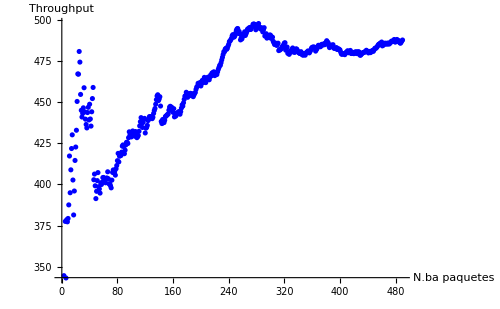
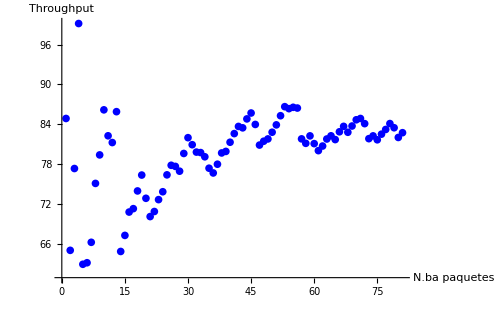
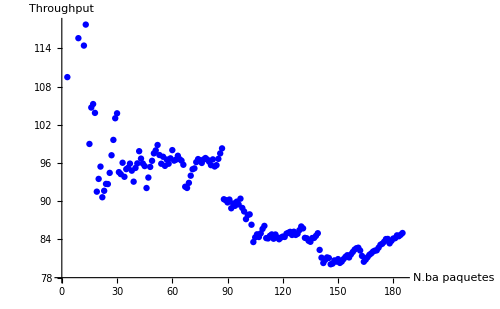
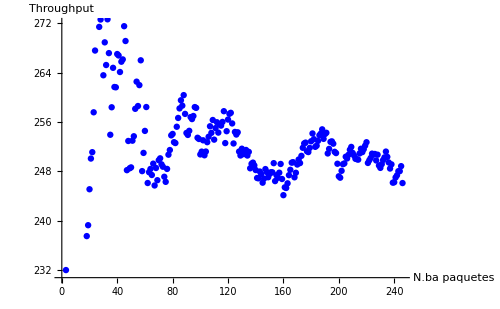
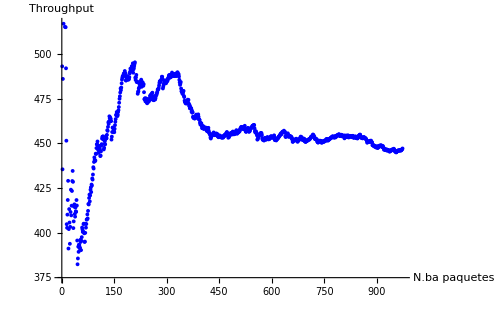
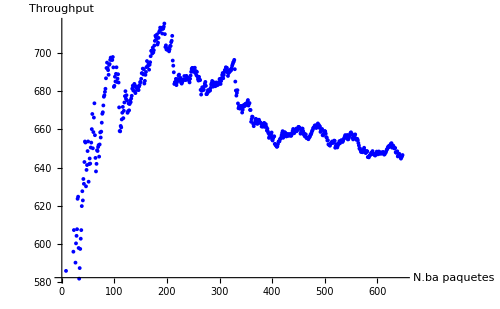
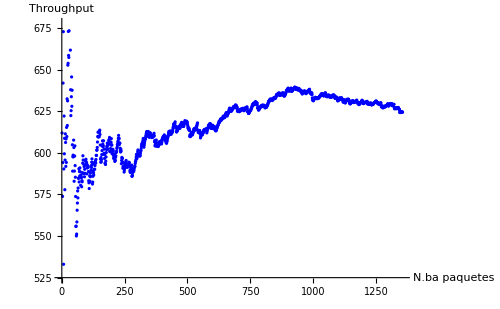
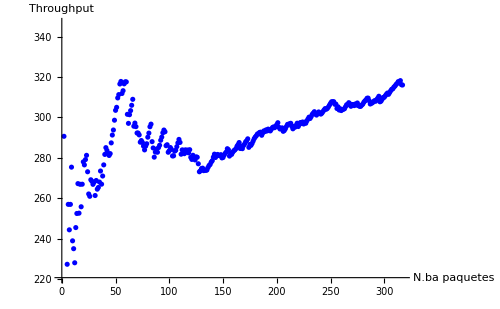
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10
```

```mathematica
ThroughputMax[paquetes123]
ThroughputMax[paquetes124]
ThroughputMax[paquetes1523]
ThroughputMax[paquetes1524]
ThroughputMax[paquetes154]
ThroughputMax[paquetes23]
ThroughputMax[paquetes24]
ThroughputMax[paquetes523]
ThroughputMax[paquetes524]
ThroughputMax[paquetes54] 
Last[paquetes123]
Last[paquetes123][[9]]
Length[paquetes123]
(Length[paquetes123]/Last[paquetes123][[1]])//N
```

487.753

447.169

82.7336

84.9989

246.115

646.63

624.456

316.058

329.895

1000.72

{1.00461,478.554,1536,0,0,1974,1,{Ori-1,2,3},0.998731}

0.998731

490

487.753

# 7B.- Obtención de estadísticas y representación gráfica de resultados parciales CON protocolo S&W

```mathematica
(*Ejecución de la función*)
opcionesDistintas3SW=ObtenerOpcionesDistintas[out3SW]
opcionesDistintas4SW=ObtenerOpcionesDistintas[out4SW]

paquetes123SW = getPacketsWithRoute[out3SW,{"Ori-1",2,3}];
paquetes1523SW = getPacketsWithRoute[out3SW,{"Ori-1",5,2,3}];
paquetes1524SW = getPacketsWithRoute[out4SW,{"Ori-1",5,2,4}];
paquetes154SW = getPacketsWithRoute[out4SW,{"Ori-1",5,4}];
paquetes124SW = getPacketsWithRoute[out4SW,{"Ori-1",2,4}]; 
paquetes23SW= getPacketsWithRoute[out3SW,{"Ori-2",2,3}];
paquetes24SW = getPacketsWithRoute[out4SW,{"Ori-2",2,4}]; 
paquetes523SW = getPacketsWithRoute[out3SW,{"Ori-5",5,2,3}];
paquetes524SW = getPacketsWithRoute[out4SW,{"Ori-5",5,2,4}]; 
paquetes54SW = getPacketsWithRoute[out4SW,{"Ori-5",5,4}]; 

tot1SW = Length[out3SW]+Length[out4SW]
tot2SW = Length[paquetes123SW]+ Length[paquetes1523SW]+Length[paquetes154SW]+Length[paquetes1524SW]+ Length[paquetes124SW]+Length[paquetes23SW]+Length[paquetes24SW]+Length[paquetes523SW]+Length[paquetes524SW]+Length[paquetes54SW]
```

{{Ori-2,2,3},{Ori-5,5,2,3},{Ori-1,5,2,3},{Ori-1,2,3}}

{{Ori-2,2,4},{Ori-5,5,4},{Ori-1,5,2,4},{Ori-1,2,4},{Ori-1,5,4},{Ori-5,5,2,4}}

6033

6033

```mathematica
t123 = getRetardo[paquetes123SW]
t124= getRetardo[paquetes124SW]
t1523 = getRetardo[paquetes1523SW]
t1524 = getRetardo[paquetes1524SW]
t154 = getRetardo[paquetes154SW]
t23 = getRetardo[paquetes23SW]
t24 = getRetardo[paquetes24SW]
t523 = getRetardo[paquetes523SW]
t524 = getRetardo[paquetes524SW]
t54 = getRetardo[paquetes54SW]
```

0.0286727

0.536063

0.367037

1.07743

0.306942

0.0278637

0.554197

0.20493

0.886626

0.145287

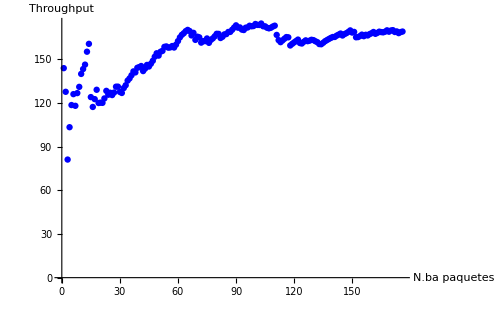
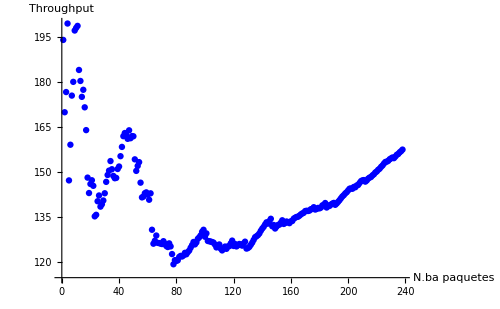
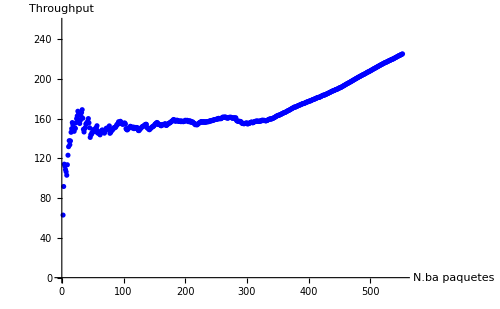
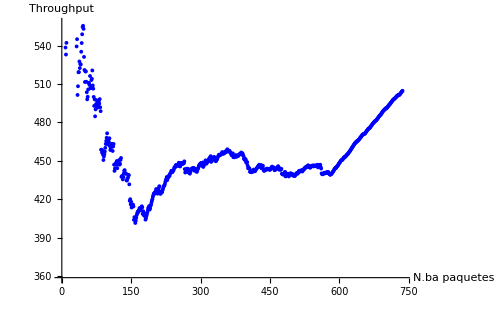
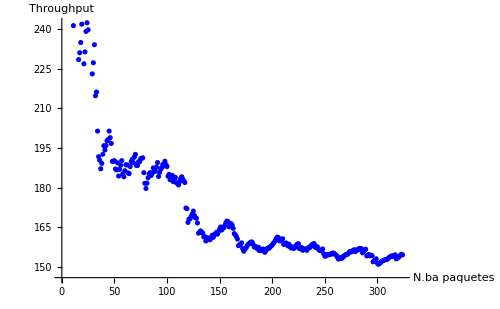
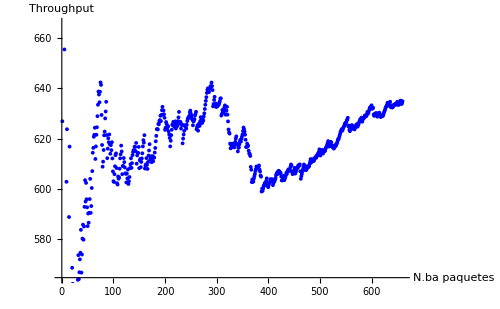
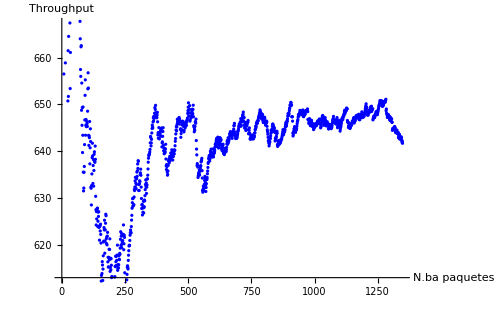
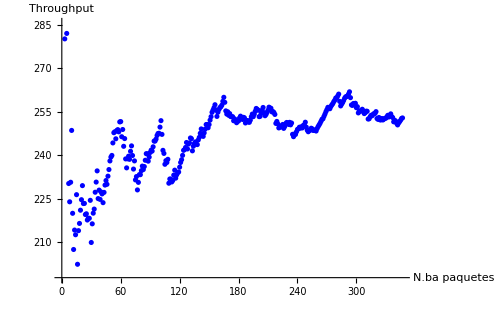
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10SW=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10SW
```

```mathematica
ThroughputMax[paquetes123SW]
ThroughputMax[paquetes124SW]
ThroughputMax[paquetes1523SW]
ThroughputMax[paquetes1524SW]
ThroughputMax[paquetes154SW]
ThroughputMax[paquetes23SW]
ThroughputMax[paquetes24SW]
ThroughputMax[paquetes523SW]
ThroughputMax[paquetes524SW]
ThroughputMax[paquetes54SW]
```

169.197

154.629

157.484

225.301

504.774

634.842

641.673

252.864

280.621

753.398

# 7C.- Obtención de estadísticas y representación gráfica de resultados parciales CON protocolo GBN

```mathematica
(*Ejecución de la función*)
opcionesDistintas3GBN=ObtenerOpcionesDistintas[out3GBN]
opcionesDistintas4GBN=ObtenerOpcionesDistintas[out4GBN]

paquetes123GBN = getPacketsWithRoute[out3GBN,{"Ori-1",2,3}];
paquetes1523GBN = getPacketsWithRoute[out3GBN,{"Ori-1",5,2,3}];
paquetes1524GBN = getPacketsWithRoute[out4GBN,{"Ori-1",5,2,4}];
paquetes154GBN = getPacketsWithRoute[out4GBN,{"Ori-1",5,4}];
paquetes124GBN = getPacketsWithRoute[out4GBN,{"Ori-1",2,4}]; 
paquetes23GBN= getPacketsWithRoute[out3GBN,{"Ori-2",2,3}];
paquetes24GBN = getPacketsWithRoute[out4GBN,{"Ori-2",2,4}]; 
paquetes523GBN = getPacketsWithRoute[out3GBN,{"Ori-5",5,2,3}];
paquetes524GBN = getPacketsWithRoute[out4GBN,{"Ori-5",5,2,4}]; 
paquetes54GBN = getPacketsWithRoute[out4GBN,{"Ori-5",5,4}]; 

tot1GBN = Length[out3GBN]+Length[out4GBN]
tot2GBN = Length[paquetes123GBN]+ Length[paquetes1523GBN]+Length[paquetes154GBN]+Length[paquetes1524GBN]+ Length[paquetes124GBN]+Length[paquetes23GBN]+Length[paquetes24GBN]+Length[paquetes523GBN]+Length[paquetes524GBN]+Length[paquetes54GBN]
```

{{Ori-2,2,3},{Ori-1,2,3},{Ori-5,5,2,3},{Ori-1,5,2,3}}

{{Ori-5,5,2,4},{Ori-1,5,4},{Ori-1,2,4},{Ori-5,5,4},{Ori-2,2,4},{Ori-1,5,2,4}}

6004

6004

```mathematica
t123 = getRetardo[paquetes123GBN]
t124= getRetardo[paquetes124GBN]
t1523 = getRetardo[paquetes1523GBN]
t1524 = getRetardo[paquetes1524GBN]
t154 = getRetardo[paquetes154GBN]
t23 = getRetardo[paquetes23GBN]
t24 = getRetardo[paquetes24GBN]
t523 = getRetardo[paquetes523GBN]
t524 = getRetardo[paquetes524GBN]
t54 = getRetardo[paquetes54GBN]
```

0.301681

0.00556125

0.300462

0.005515

0.00245332

0.316607

0.00274956

0.315885

0.00426995

0.00156224

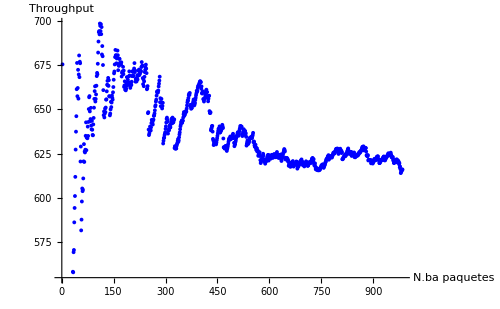
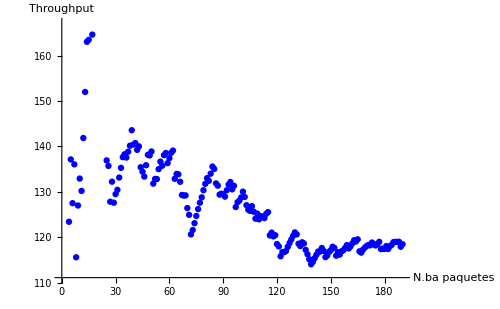
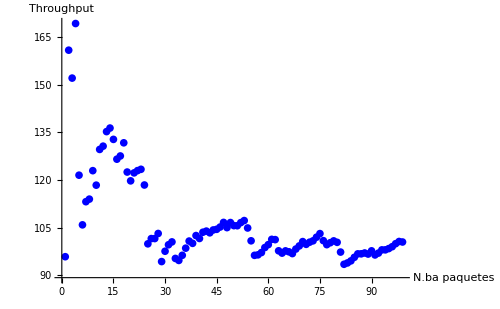
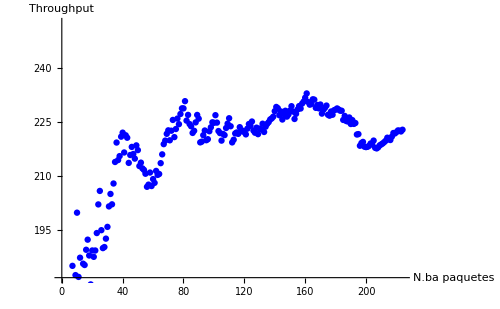
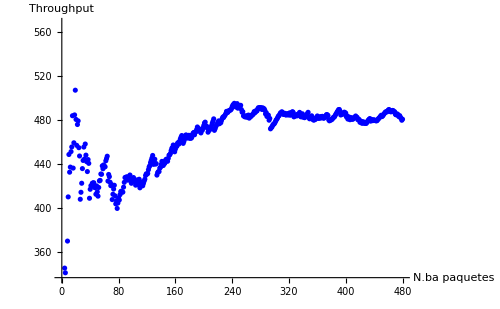
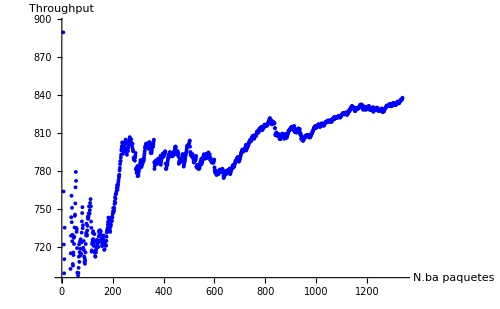
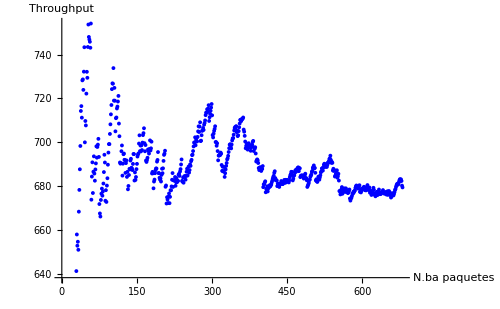
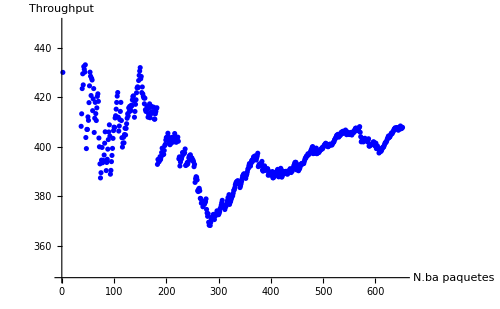
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10GBN=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10GBN
```

```mathematica
ThroughputMax[paquetes123GBN]
ThroughputMax[paquetes124GBN]
ThroughputMax[paquetes1523GBN]
ThroughputMax[paquetes1524GBN]
ThroughputMax[paquetes154GBN]
ThroughputMax[paquetes23GBN]
ThroughputMax[paquetes24GBN]
ThroughputMax[paquetes523GBN]
ThroughputMax[paquetes524GBN]
ThroughputMax[paquetes54GBN]
```

616.016

480.453

118.456

100.452

222.865

837.684

679.498

407.908

346.658

1007.7